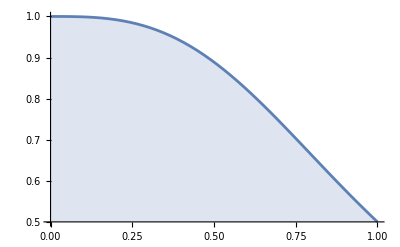

```mathematica
Plot[1/(x^3+1),{x,0,1},Filling->Axis]
```

```mathematica
Show[%1,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
f[x_]:=PDF[LaplaceDistribution[0,1],x]
F[x_]:=CDF[LaplaceDistribution[0,1],x]
```

```mathematica
f
```

f

```mathematica
integral[mu_]:=NIntegrate[f[x]*F[x-mu],{x,-Infinity,Infinity}]
```

```mathematica
integral[0.5]
```

0.379082

```mathematica
integral[9]/integral[7]
```

0.16541

```mathematica
integral[5000]/integral[5002]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
f[x_]:=1/2*Exp[-Abs[x]]
F[x_]:=Piecewise[{{1/2*(1+Exp[x]),x<0},{1/2*(1+1-Exp[-x]),x>=0}}]
```

```mathematica
f(5)
```

5 f

```mathematica
f[5]
```

1/(2 ⅇ^5)

```mathematica
f[2]
```

1/(2 ⅇ^2)

```mathematica
f[300]
```

1/(2 ⅇ^300)

```mathematica
integral[mu_]:=Integrate[f[x]*F[x-mu],{x,-Infinity,mu}]+Integrate[f[x]*F[x-mu],{x,mu,Infinity}]
```

```mathematica
integral[2]
```

3/(8 ⅇ^2)+(3+4 ⅇ^2)/(8 ⅇ^2)

```mathematica
Simplify[integral[mu]]
```

Integrate::pwrl: Unable to prove that integration limits {mu} are real. Adding assumptions may help.

∫_mu^∞ 1/2 ⅇ^(-Abs[x]) (Piecewise[{{1/2 (1+ⅇ^(-mu+x)), x<mu}, {1-ⅇ^(mu-x)/2, x≥mu}, {0, True}}])ⅆx+∫_(-∞)^mu 1/2 ⅇ^(-Abs[x]) (Piecewise[{{1/2 (1+ⅇ^(-mu+x)), x<mu}, {1-ⅇ^(mu-x)/2, x≥mu}, {0, True}}])ⅆx

```mathematica
integral[500123]
```

3/(8 ⅇ^500123)+(1000245+4 ⅇ^500123)/(8 ⅇ^500123)

```mathematica
integral[mu_]:=Integrate[f[x]*F[x-mu],{x,-Infinity,Infinity}]
```

```mathematica
Simplify[integral[mu]]
```

Piecewise[{{1/4 ⅇ^-mu (1+2 ⅇ^mu+mu), mu≥0}, {1+1/4 ⅇ^mu (-1+mu), True}}]

```mathematica
integral[mu] := Integrate[f[x] * F[x-mu]^2 * (1 - F[x]), {x, -Infinity, Infinity}]
```

```mathematica
g[mu_] := Simplify[integral[mu]]
h[mu_] := g[mu] / g[mu + 2]
```

```mathematica
Simplify[h[mu]]
```

(1/2+3/(4 ⅇ^2))/(1/2+5/(4 ⅇ^4))

1.15033

```mathematica
Plot[h[mu], {mu, -10, 10}]
```

-Graphics-

```mathematica
Sin[2]
```